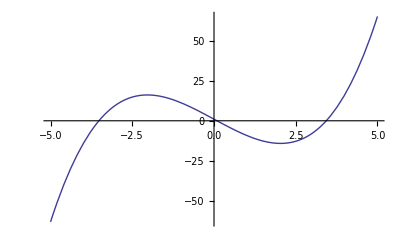

```mathematica
f[x_]:=x^3+Sin[x]-12x+1;
Plot[f[x],{x,-5,5}]
```

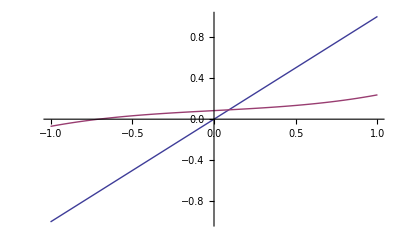

```mathematica
phi[x_]:=1/12(x^3+Sin[x]+1);
Plot[{x,phi[x]},{x,-1,1}]
```

```mathematica
z[0]:=1;
z[n_]:=phi[z[n-1]]//N;
```

```mathematica
Eps=10^(-4)/2
```

1/20000

```mathematica
n=1;
While[Abs[z[n]-z[n-1]]>Eps,Print[z[n-1]];n++]
```

1

0.236789

0.103988

0.0920771

0.0910606